```mathematica
2-2
```

0

# Quantum Motion of a Particle in a Box

Nicholas Wheeler
Reed College Physics Department
13 August 2008

### Introduction

It is by way of preparation for discussion of "quantum Liossajous figures" and "quantum vorticity" that I look here to aspects—specifically, dynamics aspects—of the simplest and most familiar of all quantum mechanical systems: the "particle-in-a-box" problem. I work first in one dimension, then by straightforward generalization in two dimensions.

One-dimensional theory

The simple essentials of the subject at hand are treated in §2.2 (pages 30–37) of Griffiths' Introduction to Quantum Mechanics (2nd edition, 2005). Some of what I will have to say parallels work reported in Cimarron Wortham's Reed College thesis: "Motion of launched wave packets in the infinite square well" (2004).

We are interested in properties of the solutions of

-ℏ^2/(2m)∂_(x,x) ψ[x,t]=ⅈ ℏ ∂_t ψ[x,t]

that conform to the boundary conditions

ψ[0,t]=ψ[a,t]    :    all  t

If we adopt units in which

ℏ=2m=a=1

we have

-∂_(x,x) ψ[x,t]=ⅈ  ∂_t ψ[x,t]
ψ[0,t]=ψ[1,t]    :    all  t

which is easier to work with. If we assume the wave function to have separated structure

ψ[x,t]=Ψ[x]*ⅇ^(-ⅈ ω t)

we find ourselves looking for solutions of

-∂_(x,x) Ψ[x]=ω Ψ[x]
 Ψ[0]= Ψ[1]=0

and are led immediately to the orthonormal eigenfunctions

```mathematica
Ψ[x_,n_]:=√2 Sin[n π x]
```

```mathematica
Table[∫_0^1 Ψ[x,m]Ψ[x,n]ⅆx,{m,1,4},{n,1,4}]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

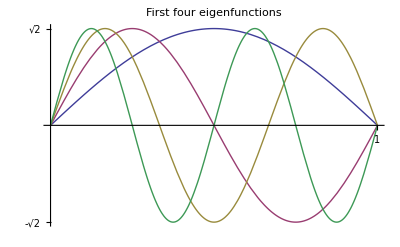

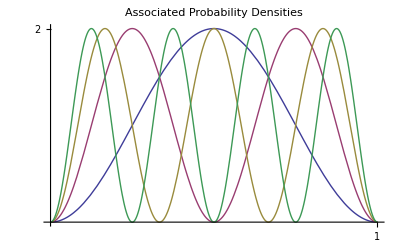

```mathematica
Plot[{Ψ[x,1],Ψ[x,2],Ψ[x,3],Ψ[x,4]}, {x,0,1},Ticks->{{1},{√2,-√2}},AxesLabel->{"x"}, LabelStyle->Directive[Bold], PlotLabel->"First four eigenfunctions"]
Plot[{Ψ[x,1]^2,Ψ[x,2]^2,Ψ[x,3]^2,Ψ[x,4]^2}, {x,0,1},Ticks->{{1},{2,-2}},AxesLabel->{"x"}, LabelStyle->Directive[Bold], PlotLabel->"Associated Probability Densities"]
```

From

```mathematica
-D[Ψ[x,n], x,x]==n^2 π^2 Ψ[x,n]
```

True

we are led to define the "eigenfrequencies"

```mathematica
ω[n_]:=n^2 π^2
```

and to construct the "buzz factors"

```mathematica
BuzzFactor[t_,n_]:=ⅇ^(-ⅈ ω[n] t)
```

The time-dependent eigenfunctions are give now by

```mathematica
ψ[x_,t_,n_]:=Ψ[x,n]*BuzzFactor[t,n]
```

which we verify:

```mathematica
-D[ψ[x,t,n], x,x]==ⅈ D[ψ[x,t,n], t]
```

True

The following figures illustrate the motion of the complex-valued functions ψ[x, t, n], {n = 1, 2}:

```mathematica
Animate[ParametricPlot3D[{{x,0,0},{0,x,0},{0,0,x},{x,Ψ[x,1]Cos[-ω[1] t/(200π)],Ψ[x,1]Sin[-ω[1] t/(200π)]}}, {x,0,1}, PlotRange->{{0,1},{-2,2},{-2,2}}, Boxed->False, Axes->False, PlotStyle->{{Thickness[.01]},{Blue},{Blue},{Red}},
PlotLabel->"Motion of ψ_1(x, t)"],{t,0,400}]

Animate[ParametricPlot3D[{{x,0,0},{0,x,0},{0,0,x},{x,Ψ[x,2]Cos[-ω[2] t/(200π)],Ψ[x,2]Sin[-ω[2] t/(200π)]}}, {x,0,1}, PlotRange->{{0,1},{-2,2},{-2,2}}, Boxed->False, Axes->False, PlotStyle->{{Thickness[.01]},{Blue},{Blue},{Red}},
PlotLabel->"Motion of ψ_2(x, t)"],{t,0,400}]
```

The functions ψ[x, t, n] move (in the sense illustrated above), but the associated probability densities are static. Observable quantum motion arises when such functions are superimposed, as an interference effect. We look to a typical (normalized) superposition:

Motion of a simple superposition

```mathematica
ψ[x_,t_]:=√(2/3)ψ[x,t,1]+√(1/3)ψ[x,t,2]
```

```mathematica
∫_0^1 ψ[x,0]^2 ⅆx
```

1

```mathematica
ComplexExpand[ψ[x,t]]
```

(2 Cos[π^2 t] Sin[π x])/(√3)+√(2/3) Cos[4 π^2 t] Sin[2 π x]+ⅈ (-(2 Sin[π^2 t] Sin[π x])/(√3)-√(2/3) Sin[4 π^2 t] Sin[2 π x])

```mathematica
Realψ[x_,t_]:=(2 Cos[π^2 t] Sin[π x])/(√3)+√(2/3) Cos[4 π^2 t] Sin[2 π x]
Imagψ[x_,t_]:=-(2 Sin[π^2 t] Sin[π x])/(√3)-√(2/3) Sin[4 π^2 t] Sin[2 π x]
```

```mathematica
Animate[ParametricPlot3D[{{x,0,0},{0,x,0},{0,0,x},{x,Realψ[x,t/(200π)],Imagψ[x,t/(200π)]}}, {x,0,1}, PlotRange->{{0,1},{-2,2},{-2,2}}, Boxed->False, Axes->False, PlotStyle->{{Thickness[.01]},{Blue},{Blue},{Red}},
PlotLabel->"Motion of a Simple Superposition"],{t,0,400}]
```

```mathematica
Animate[Plot[Realψ[x,t/(200π)]^2+Imagψ[x,t/(200π)]^2,{ x,0,1},PlotLabel->"Sloshing of the Associated Probability Density"],{t,0,400}]
```

Motion of a more complex superposition

We acquire need at this point of the "beta distribution"

```mathematica
PDF[BetaDistribution[α,β],x]
```

((1-x)^(-1+β) x^(-1+α))/Beta[α,β]

which is defined for all real non-negative values of α and β, and clearly vanishes at both ends of the unit interval:

```mathematica
PDF[BetaDistribution[α,β],0]
PDF[BetaDistribution[α,β],1]
```

0^(-1+α)/Beta[α,β]

0^(-1+β)/Beta[α,β]

and in between manages for many (α, β) values to look quite "Gaussian":

```mathematica
Manipulate[Plot[PDF[BetaDistribution[α,β],x], {x,0,1}, PlotRange->{0,12},PlotLabel->"Parameter Dependence of the β Distribution"], {α,2,100},{β,2,100}]
```

The beta distribution provides a handy description of what might be called a "boxed Gaussian"—a normal distribution with its boundary-condition-violating tails cut off. (Wortham supplies a proof (pages 10–12 of his Reed thesis) that the beta distribution—despite its purely algebraic structure—becomes Gaussian in the small-variance limit.)

Let us look to the quantum motion that evolves from the initially real-valued wavefunction

```mathematica
Initialψ[x_]:=√PDF[BetaDistribution[50,100],x]
```

```mathematica
Mean[BetaDistribution[50,100]]
√Variance[BetaDistribution[50,100]]//N
```

1/3

0.0383624

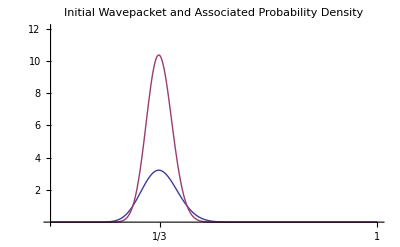

```mathematica
Plot[{Initialψ[x],Initialψ[x]^2},{x,0,1}, PlotRange->{0,12}, Ticks->{{1/3,1},{2,4,6,8,10,12}},PlotLabel->"Initial Wavepacket and Associated Probability Density"]
```

To launch such a wavepacket into motion, we write it as a weighted sum of eigenfunctions,  and then set each of those abuzz:

```mathematica
Coefficients=Table[{n,NIntegrate[Initialψ[x]*Ψ[x,n],{x,0,1}]},{n,1,40}]
```

{{1,0.529988},{2,0.502007},{3,-0.00937532},{4,-0.430639},{5,-0.37031},{6,0.00499618},{7,0.265634},{8,0.214893},{9,0.00658807},{10,-0.121678},{11,-0.0983593},{12,-0.0117822},{13,0.0394282},{14,0.034886},{15,0.0086875},{16,-0.00783355},{17,-0.00902084},{18,-0.0037283},{19,0.000342324},{20,0.0014294},{21,0.000936346},{22,0.000281021},{23,-0.0000438851},{24,-0.000105122},{25,-0.0000692241},{26,-0.000028446},{27,-6.20016×10^-6},{28,1.63774×10^-6},{29,2.82048×10^-6},{30,2.02155×10^-6},{31,1.09376×10^-6},{32,4.88056×10^-7},{33,1.76035×10^-7},{34,4.12622×10^-8},{35,-6.12663×10^-9},{36,-1.68946×10^-8},{37,-1.51077×10^-8},{38,-1.05731×10^-8},{39,-6.56926×10^-9},{40,-3.7824×10^-9}}

```mathematica
ResolvedInitialψ[x_]:=∑_(n=1)^31 Coefficients⟦n⟧⟦2⟧Ψ[x,n]
```

The following figure

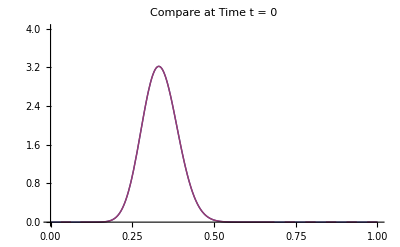

```mathematica
Plot[{Initialψ[x],ResolvedInitialψ[x]},{x,0,1}, PlotRange->{0,4},PlotLabel->"Compare at Time t = 0"]
```

provides convincing evidence that our  ResolvedInitialψ[x] does indeed provide an excellent approximation to Initialψ[x]. As also does the following proof of normalization:

```mathematica
NIntegrate[ResolvedInitialψ[x]^2,{x,0,1}]
```

1.

If we now turn on the buzz factors we are led to define

```mathematica
Evolvedψ[x_,t_]:=∑_(n=1)^31 Coefficients⟦n⟧⟦2⟧ψ[x,t,n]
```

The complex-valued function thus defined is fairly complicated:

```mathematica
ComplexExpand[Evolvedψ[x,t]]
```

0.749516 Cos[π^2 t] Sin[π x]+0.709945 Cos[4 π^2 t] Sin[2 π x]-0.0132587 Cos[9 π^2 t] Sin[3 π x]-0.609015 Cos[16 π^2 t] Sin[4 π x]-0.523697 Cos[25 π^2 t] Sin[5 π x]+0.00706566 Cos[36 π^2 t] Sin[6 π x]+0.375664 Cos[49 π^2 t] Sin[7 π x]+0.303905 Cos[64 π^2 t] Sin[8 π x]+0.00931694 Cos[81 π^2 t] Sin[9 π x]-0.172079 Cos[100 π^2 t] Sin[10 π x]-0.139101 Cos[121 π^2 t] Sin[11 π x]-0.0166626 Cos[144 π^2 t] Sin[12 π x]+0.0557599 Cos[169 π^2 t] Sin[13 π x]+0.0493363 Cos[196 π^2 t] Sin[14 π x]+0.012286 Cos[225 π^2 t] Sin[15 π x]-0.0110783 Cos[256 π^2 t] Sin[16 π x]-0.0127574 Cos[289 π^2 t] Sin[17 π x]-0.00527261 Cos[324 π^2 t] Sin[18 π x]+0.00048412 Cos[361 π^2 t] Sin[19 π x]+0.00202148 Cos[400 π^2 t] Sin[20 π x]+0.00132419 Cos[441 π^2 t] Sin[21 π x]+0.000397424 Cos[484 π^2 t] Sin[22 π x]-0.0000620629 Cos[529 π^2 t] Sin[23 π x]-0.000148666 Cos[576 π^2 t] Sin[24 π x]-0.0000978977 Cos[625 π^2 t] Sin[25 π x]-0.0000402287 Cos[676 π^2 t] Sin[26 π x]-8.76836×10^-6 Cos[729 π^2 t] Sin[27 π x]+2.31611×10^-6 Cos[784 π^2 t] Sin[28 π x]+3.98877×10^-6 Cos[841 π^2 t] Sin[29 π x]+2.85891×10^-6 Cos[900 π^2 t] Sin[30 π x]+1.54681×10^-6 Cos[961 π^2 t] Sin[31 π x]+ⅈ (-0.749516 Sin[π^2 t] Sin[π x]-0.709945 Sin[4 π^2 t] Sin[2 π x]+0.0132587 Sin[9 π^2 t] Sin[3 π x]+0.609015 Sin[16 π^2 t] Sin[4 π x]+0.523697 Sin[25 π^2 t] Sin[5 π x]-0.00706566 Sin[36 π^2 t] Sin[6 π x]-0.375664 Sin[49 π^2 t] Sin[7 π x]-0.303905 Sin[64 π^2 t] Sin[8 π x]-0.00931694 Sin[81 π^2 t] Sin[9 π x]+0.172079 Sin[100 π^2 t] Sin[10 π x]+0.139101 Sin[121 π^2 t] Sin[11 π x]+0.0166626 Sin[144 π^2 t] Sin[12 π x]-0.0557599 Sin[169 π^2 t] Sin[13 π x]-0.0493363 Sin[196 π^2 t] Sin[14 π x]-0.012286 Sin[225 π^2 t] Sin[15 π x]+0.0110783 Sin[256 π^2 t] Sin[16 π x]+0.0127574 Sin[289 π^2 t] Sin[17 π x]+0.00527261 Sin[324 π^2 t] Sin[18 π x]-0.00048412 Sin[361 π^2 t] Sin[19 π x]-0.00202148 Sin[400 π^2 t] Sin[20 π x]-0.00132419 Sin[441 π^2 t] Sin[21 π x]-0.000397424 Sin[484 π^2 t] Sin[22 π x]+0.0000620629 Sin[529 π^2 t] Sin[23 π x]+0.000148666 Sin[576 π^2 t] Sin[24 π x]+0.0000978977 Sin[625 π^2 t] Sin[25 π x]+0.0000402287 Sin[676 π^2 t] Sin[26 π x]+8.76836×10^-6 Sin[729 π^2 t] Sin[27 π x]-2.31611×10^-6 Sin[784 π^2 t] Sin[28 π x]-3.98877×10^-6 Sin[841 π^2 t] Sin[29 π x]-2.85891×10^-6 Sin[900 π^2 t] Sin[30 π x]-1.54681×10^-6 Sin[961 π^2 t] Sin[31 π x])

We isolate the real and imaginary parts

```mathematica
RealEvolvedψ[x_,t_]:=ComplexExpand[Re[Evolvedψ[x,t]]]
ImagEvolvedψ[x_,t_]:=ComplexExpand[Im[Evolvedψ[x,t]]]
```

and use that information to construct a display of the motion of the complex-valued wavepacket:

```mathematica
Manipulate[ParametricPlot3D[{{x,0,0},{0,x,0},{0,0,x},{x,RealEvolvedψ[x,t/(200π)],ImagEvolvedψ[x,t/(200π)]}}, {x,0,1}, PlotRange->{{0,1},{-3,3},{-3,3}}, Boxed->False, Axes->False, PlotStyle->{{Thickness[.01]},{Blue},{Blue},{Red}}],{t,0,400,1}]
```

The animation demonstrates, by the way, the recurrence that follows from the fact that

```mathematica
ω[n]==n^2 ω[1]
```

True

The equation shows that the n^th mode completes n^2 cycles in the time it takes the fundamental mode to complete one. Any wavepacket assembled from such buzzing eigenfunctions therefore will return periodically to its original form, the recurrence time being given by

```mathematica
Subscript[T, recurrence]=(2π)/ω[1]
```

2/π

Here is a more "physical" derivation of the same result:

T_recurrence=(2π)/ω[1]=(2π ℏ)/GroundstateEnergy=2π ℏ((π^2 ℏ^2)/(2m a^2))^-1

```mathematica
Simplify[2π ℏ((π^2 ℏ^2)/(2m a^2))^-1]/.{ℏ->1, a->1,m->1/2}
```

2/π

All the complicated phase information—evident in the preceding figure—is lost when we construct the moving probability density (which itself is quite complicated, and again shows recurrence):

```mathematica
EvolvedProbabilityDensity[x_,t_]:=RealEvolvedψ[x,t]^2+ImagEvolvedψ[x,t]^2
```

```mathematica
Manipulate[Plot[Evaluate[EvolvedProbabilityDensity[x,1/600 Subscript[T, recurrence] n]],{x,0,1},PlotRange->{0,12},PlotLabel->"Motion of the Probability Density"],{n,0,600,1}]
```

Using that moving distribution to compute the moving expected position (this will take about a minute)

```mathematica
Evaluate[NIntegrate[Re[x*EvolvedProbabilityDensity[x,1/600 Subscript[T, recurrence] 110]],{x,0,1}]]
```

0.636413

```mathematica
ExpectedPositionData=Table[NIntegrate[Re[x*EvolvedProbabilityDensity[x,1/600 Subscript[T, recurrence]  n]],{x,0,1}],{n,0,600,1}];
```

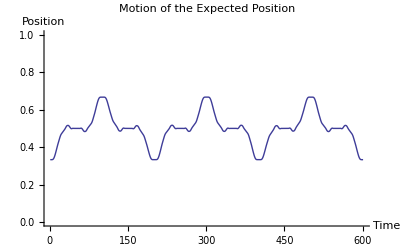

```mathematica
ListPlot[ExpectedPositionData, Joined->True, PlotRange->{0,1},PlotLabel->"Motion of the Expected Position", AxesLabel->{"Time","Position"}]
```

Consider the enormous amount of information that has been discarded in the construction of the preceding figure—phase information which could never be reconstructed on the basis of the figure. 

We work in units in which the recurrence time is 600. It is curious, therefore, that the expected position executes (in this instance) three cycles during the span of a single recurrence cycle. The following superposition of figures casts some light on the situation

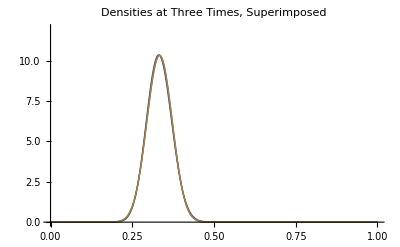

```mathematica
Plot[{EvolvedProbabilityDensity[x,0/3 2/π],EvolvedProbabilityDensity[x,1/3 2/π],EvolvedProbabilityDensity[x,2/3 2/π]},{x,0,1},PlotRange->{0,12},PlotLabel->"Densities at Three Times, Superimposed"]
```

and the following figure casts an even brighter light:

```mathematica
Table[{"T_recursion/3"k,ParametricPlot3D[{{x,0,0},{0,x,0},{0,0,x},{x,RealEvolvedψ[x, 2/(3π)k],ImagEvolvedψ[x, 2/(3π)k]}}, {x,0,1}, PlotRange->{{0,1},{-3,3},{-3,3}}, Boxed->False, Axes->False, PlotStyle->{{Thickness[.01]},{Blue},{Blue},{Red}}]},{k,0,2,1}]//TableForm
```

0 | -Graphics3D-
T_recursion/3 | -Graphics3D-
2 T_recursion/3 | -Graphics3D-

Launched wavepackets

We have been working thus far with a wavepacket that was initially at rest, in the sense that initially ⟨p⟩ = 0, as I attempt to demonstrate: recalling that we have set ℏ = 1, we have

```mathematica
InitiallyExpectedMomentum=-ⅈ NIntegrate[ResolvedInitialψ[x]D[ResolvedInitialψ[x],x],{x,0,1}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.353531}. NIntegrate obtained 4.996×10^-16 and 1.59695×10^-15 for the integral and error estimates.

```mathematica
InitiallyExpectedMomentum
```

0. ⅈ

…which is to say (if we disregard Mathematica's complaint): the expected value of the momentum is zero.

To "launch" such a wavepacket, one hits it with the complex multiplier

ⅇ^(ⅈ/ℏ p x)    :    p=m v

which in our units becomes

```mathematica
ⅇ^(ⅈ/ℏ p x)/.{ℏ->1, p->1/2 v}
```

ⅇ^((ⅈ v x)/2)

Suppose we were to set v = 300:

```mathematica
ⅇ^((ⅈ v x)/2)/.v->300
```

ⅇ^(150 ⅈ x)

Hitting a real-valued initial state with such a "launch factor" produces a complex-valued initial state, as illustrated below:

```mathematica
ParametricPlot3D[{{x,0,0},{0,x,0},{0,0,x},{x,ResolvedInitialψ[x]*Cos[150x],ResolvedInitialψ[x]*Sin[150x]}}, {x,0,1}, PlotRange->{{0,1},{-4,4},{-4,4}}, Boxed->False, Axes->False, PlotStyle->{{Thickness[.01]},{Blue},{Blue},{Red}},
PlotLabel->"Launched (∴ Complexified) Initial State"]
```

-Graphics3D-

The initial expected value of the momentum has now the non-zero value

```mathematica
InitialLaunchedMomentum=-ⅈ  NIntegrate[ResolvedInitialψ[x]*ⅇ^(-ⅈ 150 x)D[ResolvedInitialψ[x]*ⅇ^(ⅈ 150 x),x],{x,0,1}];
```

```mathematica
InitialLaunchedMomentum
```

150.-4.95831×10^-9 ⅈ

```mathematica
InitialLaunchedψ[x_]:=ⅇ^(ⅈ 150 x)*Initialψ[x]
```

Experiment (see below) shows that the coefficients that contribute most importantly to the resolution of a launched wavepacket have orders in  the range

momentum/π±20

In the present instance we have

```mathematica
150/π//N
```

47.7465

so (to establish the point) we look at

```mathematica
NIntegrate[Ψ[x,28]*InitialLaunchedψ[x],{x,0,1}]
NIntegrate[Ψ[x,48]*InitialLaunchedψ[x],{x,0,1}]
NIntegrate[Ψ[x,68]*InitialLaunchedψ[x],{x,0,1}]
```

-0.000687937+0.000745642 ⅈ

0.0815697+0.297944 ⅈ

0.000691565+0.000295293 ⅈ

We construct a complete set of "launched coefficients"

```mathematica
LaunchedCoefficients=Table[NIntegrate[Ψ[x,n]*InitialLaunchedψ[x],{x,0,1}],{n,28,68}]
```

{-0.000687937+0.000745642 ⅈ,0.000195104+0.00178325 ⅈ,0.00257632+0.00169251 ⅈ,0.00487627-0.00163235 ⅈ,0.00263654-0.0078938 ⅈ,-0.00761018-0.010618 ⅈ,-0.0198835+0.000237762 ⅈ,-0.0161644+0.0245012 ⅈ,0.0165771+0.038616 ⅈ,0.0575683+0.00959469 ⅈ,0.0521934-0.0588269 ⅈ,-0.0297334-0.0984525 ⅈ,-0.126469-0.0324085 ⅈ,-0.114133+0.113435 ⅈ,0.0477043+0.186611 ⅈ,0.215394+0.0612748 ⅈ,0.181595-0.176071 ⅈ,-0.0684553-0.269006 ⅈ,-0.28532-0.0788035 ⅈ,-0.217203+0.216593 ⅈ,0.0815697+0.297944 ⅈ,0.292948+0.0747175 ⅈ,0.19968-0.206901 ⅈ,-0.0743423-0.255142 ⅈ,-0.231891-0.0564086 ⅈ,-0.144064+0.150336 ⅈ,0.0482664+0.169743 ⅈ,0.140465+0.0370228 ⅈ,0.0831708-0.0810176 ⅈ,-0.0200492-0.0878401 ⅈ,-0.064162-0.0220978 ⅈ,-0.0387639+0.030939 ⅈ,0.00341746+0.0350004 ⅈ,0.0213265+0.0114078 ⅈ,0.0143294-0.00740926 ⅈ,0.00146529-0.0103305 ⅈ,-0.00466767-0.00458749 ⅈ,-0.00394395+0.000548814 ⅈ,-0.0012087+0.00201669 ⅈ,0.000433843+0.00127665 ⅈ,0.000691565+0.000295293 ⅈ}

```mathematica
Length[LaunchedCoefficients]
```

41

which are now complex. We separate their real from their imaginary parts

```mathematica
RealPartsLaunchedCoefficients=Table[Re[LaunchedCoefficients⟦k⟧],{k,1,41}]
ImagPartsLaunchedCoefficients=Table[Im[LaunchedCoefficients⟦k⟧],{k,1,41}]
```

{-0.000687937,0.000195104,0.00257632,0.00487627,0.00263654,-0.00761018,-0.0198835,-0.0161644,0.0165771,0.0575683,0.0521934,-0.0297334,-0.126469,-0.114133,0.0477043,0.215394,0.181595,-0.0684553,-0.28532,-0.217203,0.0815697,0.292948,0.19968,-0.0743423,-0.231891,-0.144064,0.0482664,0.140465,0.0831708,-0.0200492,-0.064162,-0.0387639,0.00341746,0.0213265,0.0143294,0.00146529,-0.00466767,-0.00394395,-0.0012087,0.000433843,0.000691565}

{0.000745642,0.00178325,0.00169251,-0.00163235,-0.0078938,-0.010618,0.000237762,0.0245012,0.038616,0.00959469,-0.0588269,-0.0984525,-0.0324085,0.113435,0.186611,0.0612748,-0.176071,-0.269006,-0.0788035,0.216593,0.297944,0.0747175,-0.206901,-0.255142,-0.0564086,0.150336,0.169743,0.0370228,-0.0810176,-0.0878401,-0.0220978,0.030939,0.0350004,0.0114078,-0.00740926,-0.0103305,-0.00458749,0.000548814,0.00201669,0.00127665,0.000295293}

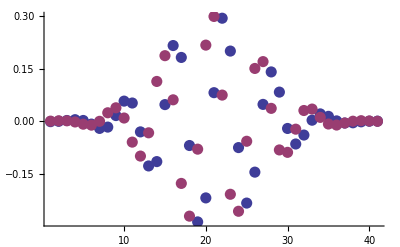

```mathematica
ListPlot[{RealPartsLaunchedCoefficients,ImagPartsLaunchedCoefficients}, PlotStyle->{PointSize[0.02],PointSize[0.02]}]
```

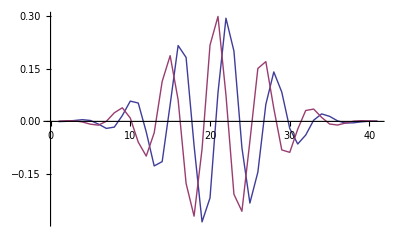

```mathematica
ListPlot[{RealPartsLaunchedCoefficients,ImagPartsLaunchedCoefficients}, Joined->True]
```

We use this information to assemble

```mathematica
MovingLaunchedψ[x_,t_]:=∑_(n=1)^41 LaunchedCoefficients⟦n⟧ψ[x,t,27+n]
```

```mathematica
RealMovingLaunchedψ[x_,t_]:=ComplexExpand[Re[MovingLaunchedψ[x,t]]]
ImagMovingLaunchedψ[x_,t_]:=ComplexExpand[Im[MovingLaunchedψ[x,t]]]
```

```mathematica
LaunchedProbabilityDensity[x_,t_]:=RealMovingLaunchedψ[x,t]^2+ImagMovingLaunchedψ[x,t]^2
```

```mathematica
UnlaunchedInitial=Plot[Evaluate[EvolvedProbabilityDensity[x,0]],{x,0,1}, PlotRange->{0,12}];
LaunchedInitial=Plot[Evaluate[LaunchedProbabilityDensity[x,0]],{x,0,1}, PlotRange->{0,12}];
```

The initial launched distribution, though assembled now from a different set of (complexly weighted) eigenstates, again reproduces quite accurately the initial unlaunced distribution:

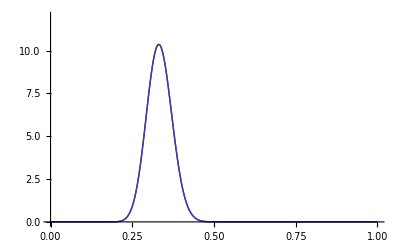

```mathematica
Show[UnlaunchedInitial,LaunchedInitial]
```

I show below the appearannce of the lunched probability density at each of 24 equally-spaced times during a single recurrence cycle:

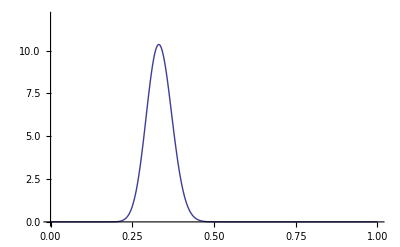
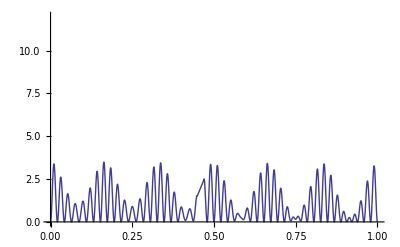
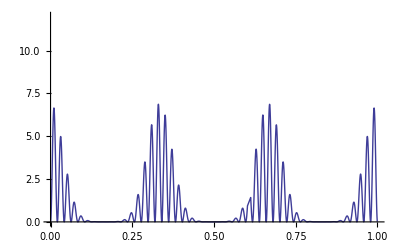
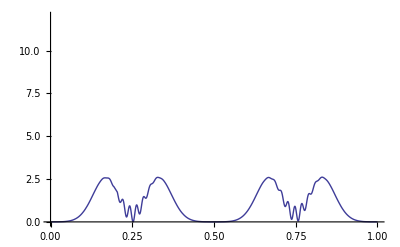
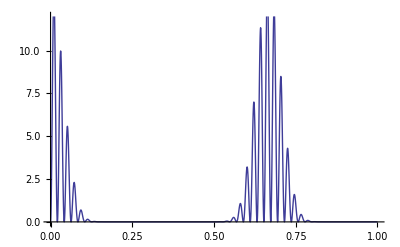
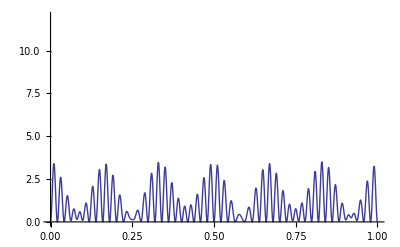
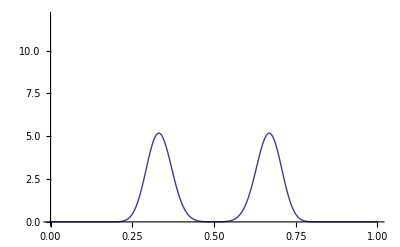
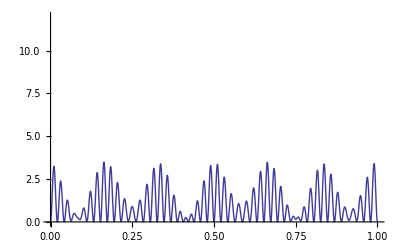
0 | -Graphics-
T_recurrence/24 | -Graphics-
2 T_recurrence/24 | -Graphics-
3 T_recurrence/24 | -Graphics-
4 T_recurrence/24 | -Graphics-
5 T_recurrence/24 | -Graphics-
6 T_recurrence/24 | -Graphics-
7 T_recurrence/24 | -Graphics-
8 T_recurrence/24 | -Graphics-
9 T_recurrence/24 | -Graphics-
10 T_recurrence/24 | -Graphics-
11 T_recurrence/24 | -Graphics-
12 T_recurrence/24 | -Graphics-
13 T_recurrence/24 | -Graphics-
14 T_recurrence/24 | -Graphics-
15 T_recurrence/24 | -Graphics-
16 T_recurrence/24 | -Graphics-
17 T_recurrence/24 | -Graphics-
18 T_recurrence/24 | -Graphics-
19 T_recurrence/24 | -Graphics-
20 T_recurrence/24 | -Graphics-
21 T_recurrence/24 | -Graphics-
22 T_recurrence/24 | -Graphics-
23 T_recurrence/24 | -Graphics-
24 T_recurrence/24 | -Graphics-

```mathematica
Table[{k"T_recurrence/24",Plot[Evaluate[LaunchedProbabilityDensity[x,2/π k/24]],{x,0,1}, PlotRange->{0,12}]}, {k,0,24,1}]//TableForm
```

The following (fairly time-consuming) calculations evaluates the expected position at each of 6000 times during a single recurrence cycle:

```mathematica
ExpectedPositionDataAfterLaunch=Table[NIntegrate[Re[x*LaunchedProbabilityDensity[x,1/600 2/π  n]],{x,0,1}],{n,0,600,1}];
```

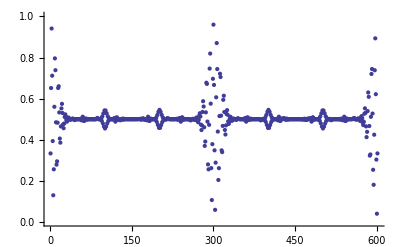

```mathematica
ListPlot[ExpectedPositionDataAfterLaunch, PlotRange->{0,1}]
```

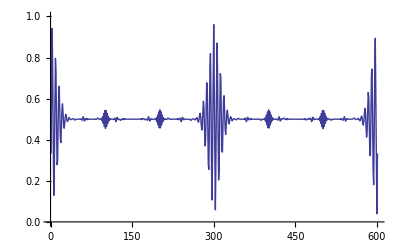

```mathematica
ListPlot[ExpectedPositionDataAfterLaunch, Joined->True,PlotRange->{0,1}]
```

One cannot help but notice the curious sub-periodicities, which I will not attempt to explain.

Quantum motion in the classical limit

Reinstating all physical parameters, we notice that the Schrödinger equation

-ℏ^2/(2m)∂_(x,x) ψ[x,t]=ⅈ ℏ ∂_t ψ[x,t]

can be written

-∂_(x,x) ψ[x,t]=ⅈ (2m)/ℏ ∂_t ψ[x,t]

which reduces to the equation with which we have been working if one adjusts the time-scale:

t→θ=ℏ/(2m)t

One expects the quantum physics to look ever more classical as one approaches the limit  m ↑ ∞  (or equivalently: ℏ ↓ 0). Which amounts to shrinking the time scale

t→θ=α t   :   α≪ 1

We have encountered the familiar fact which lies at the base of the Feynman formalism—namely, that "quantum mechanics is briefly classical." I propose therefore to look to the short-time motion of a launched wavepacket (in sufficiently long times it will execute—exactly—all the complicated gyrations described above, and will, in particular, display recurrence).

Notice in this connection that in the most recent of the preceding figures the value of ⟨x⟩ oscillates back and forth during the brief interval

0<t<20/600 T_recurrence

with seemingly constant frequency and slowly diminishing amplitude. We take a magnified look at the quantum mechanics during that interval.

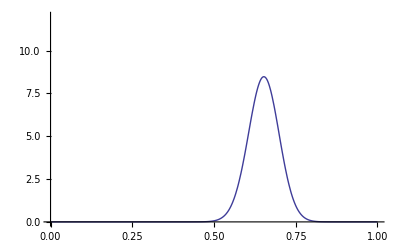
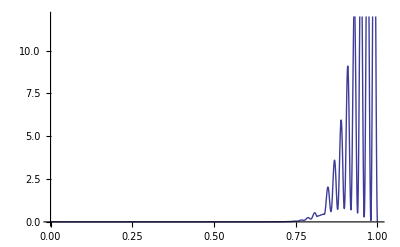
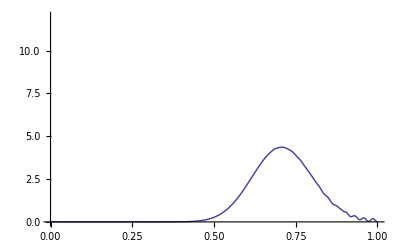
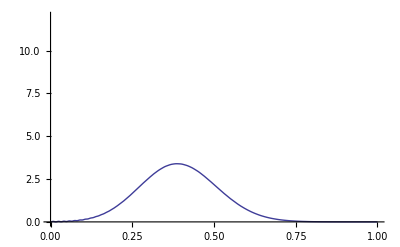
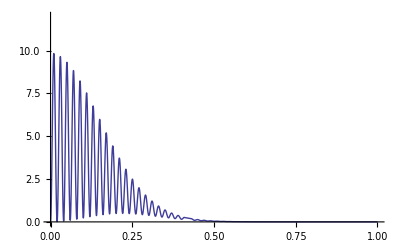
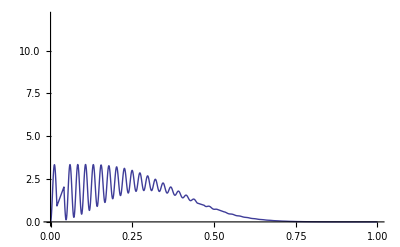
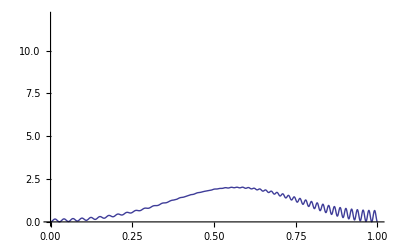
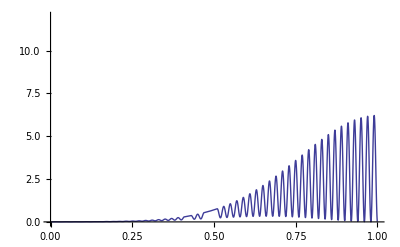
0 | -Graphics-
(T_recurrence/30)/20 | -Graphics-
(T_recurrence/30)/10 | -Graphics-
(3 T_recurrence/30)/20 | -Graphics-
(T_recurrence/30)/5 | -Graphics-
(T_recurrence/30)/4 | -Graphics-
(3 T_recurrence/30)/10 | -Graphics-
(7 T_recurrence/30)/20 | -Graphics-
(2 T_recurrence/30)/5 | -Graphics-
(9 T_recurrence/30)/20 | -Graphics-
(T_recurrence/30)/2 | -Graphics-
(11 T_recurrence/30)/20 | -Graphics-
(3 T_recurrence/30)/5 | -Graphics-
(13 T_recurrence/30)/20 | -Graphics-
(7 T_recurrence/30)/10 | -Graphics-
(3 T_recurrence/30)/4 | -Graphics-
(4 T_recurrence/30)/5 | -Graphics-
(17 T_recurrence/30)/20 | -Graphics-
(9 T_recurrence/30)/10 | -Graphics-
(19 T_recurrence/30)/20 | -Graphics-
T_recurrence/30 | -Graphics-

```mathematica
Table[{k/20"T_recurrence/30",Plot[Evaluate[LaunchedProbabilityDensity[x,2/π k/600]],{x,0,1}, PlotRange->{0,12}]}, {k,0,20,1}]//TableForm
```

```mathematica
ExpectedPositionDataShortTerm=Table[NIntegrate[Re[x*LaunchedProbabilityDensity[x,1/6000 2/π  n]],{x,0,1}],{n,0,200,1}];
```

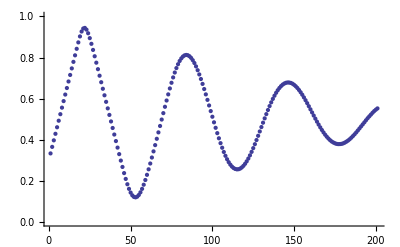

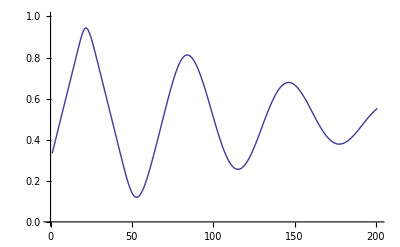

```mathematica
ListPlot[ExpectedPositionDataShortTerm, PlotRange->{0,1}]
ListPlot[ExpectedPositionDataShortTerm, PlotRange->{0,1}, Joined->True]
```

I draw attention once again to how little quantum information survives in the statement of this semi-classical result.

The figure shows the motion of the expected position during the first  200/6000=1/30 of a recurrence cycle. The period of the oscillations appears to be about 1/63 of a cycle. That number can be understood as follows: in physical variables, one has

Quantum Recurrence Time=(2π)/(ℏ(Groundstate Energy))=(4π m a^2)/(π^2 ℏ)

(Classical Period)/(Quantum Recurrence Time)=(2a)/v((4π m a^2)/(π^2 ℏ))^-1

```mathematica
Simplify[(2a)/v((4π m a^2)/(π^2 ℏ))^-1]
```

(π ℏ)/(2 a m v)

```mathematica
%/.{a->1,ℏ->1,m->1/2}
```

π/v

The computed data, on the other hand, supplies (by best informal estimate)

(Classical Period)/(Quantum Recurrence Time)=63/6000

```mathematica
Solve[π/v==63/6000,v]//N
```

{{v→299.199}}

This agrees very well with the fact that at the outset we set v = 300.